```mathematica
g=9.8; (*grav. constant*)
V = 30;
th = 50 * π / 180;
y0=2; (*20 degrees*)
yprime0 = V Sin[th]; (*starting from rest*)
x0 = 0;
xprime0=V Cos[th];
(*ϕ=y;
t=x;*)
(*ode1={x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t] ^ 2],x[0]==x0,y[0]==y0,x'[0]==xprime0, y'[0]==yprime0};
ode2 ={y''[t]==-g (1+(y'[t] / vt ^ 2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==x0,y[0]==y0,y'[0]==yprime0,x'[0]==xprime0};*)
sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==x0,y[0]==y0,x'[0]==xprime0,y'[0]==yprime0},{x, y},{t,0,200}];
```

```mathematica
myplot1 = Plot[ y[t]/.sol,{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
```

```mathematica
myplot2=Plot[x[t]/.sol,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

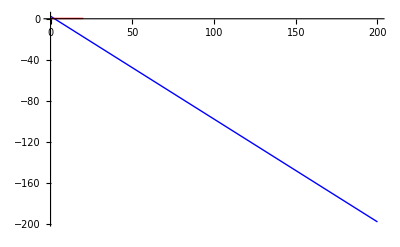

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8;
Module[
{result = NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==x0,y[0]==y0,x'[0]==xprime0,y'[0]==yprime0},{x,y},{t,0,200}]},
Plot[{ x[t],y[t]/.result},{t,0,200},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,200},{-200,200}},ImageSize->{500,300}]],
{{vt,0.5,"terminal velocity (m/s)"},0,2,Appearance->"Labeled"},{{t,1.,"time (s)"},.1,10.,Appearance->"Labeled"},
{{yprime0,0,"initial velocity (m/s)"},0.,10.,Appearance->"Labeled"},
{{th, 45 * Pi /180, "angle (rad)"}, 0., Pi, Appearance -> "Labeled"}]
```

NDSolve::dsvar: 1. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1. cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.